## First we find the transfer function

```mathematica
c=Kp+Ki/s+Kd s;
block2=1/(s^2+1)
```

1/(1+s^2)

```mathematica
ImageRotate[-Graphics-,Degree 3]
```

-Graphics-

## Define some nice functions that let us put blocks together

```mathematica
blockSeries[block1_,block2_]:=Module[
{},
Return[block1*block2]
]
```

```mathematica
blockFeedback[block1_,block2_]:=Module[
{},
Return[block1/(1+block1*block2)]
]
```

```mathematica
blockParallel[block1_,block2_]:=Module[
{},
Return[block1+block2]
]
```

## Now use the newly created functions to find the transfer function

```mathematica
tf=Simplify@blockFeedback[blockSeries[c,block2],1]
```

(Ki+s (Kp+Kd s))/(Ki+s (1+Kp+Kd s+s^2))

### Here we show the denominator of the transfer function as we will need to use it to find the poles in the next section.

```mathematica
Denominator[tf]
```

Ki+s (1+Kp+Kd s+s^2)

## Group of things for evaluation reasons

### To figure out whether or not given values of Ki, Kd, and Kp make the system stable, we need to find the poles of the transfer function. First make function that finds the poles and plots them on the complex plane.

```mathematica
findPlotPoles[tf_,params_]:=Module[{rules},
rules=N@Solve[Denominator@tf==0,s]/.params;
Print[rules];
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@(s/.rules),AspectRatio->1,PlotStyle->PointSize[.05],AxesOrigin->{0,0}]]
```

### Below we have an unstable system because we have at least one pole contains a real positive part.

{{s→-0.304969},{s→0.152485+1.03429 ⅈ},{s→0.152485-1.03429 ⅈ}}

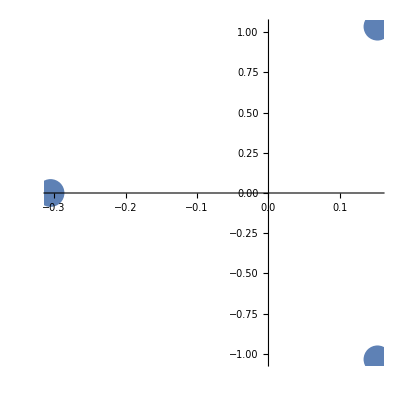

```mathematica
findPlotPoles[tf,<|Ki->1/3,Kd->0,Kp->0|>]
```

### Below we have a stable system because none of the poles have a real positive part.

{{s→-1.11022×10^-16},{s→-0.5+1.32288 ⅈ},{s→-0.5-1.32288 ⅈ}}

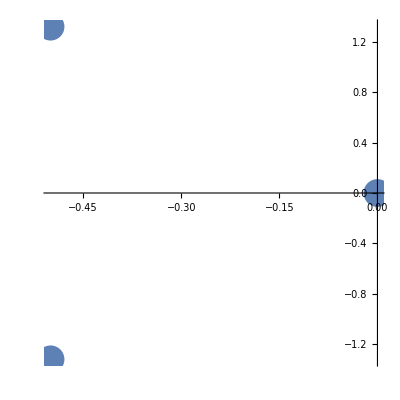

```mathematica
findPlotPoles[tf,<|Ki->0,Kd->1,Kp->1|>]
```

### Below we have a stable system because none of the poles have a real positive part.

{{s→-0.374294},{s→-0.146187+0.932307 ⅈ},{s→-0.146187-0.932307 ⅈ}}

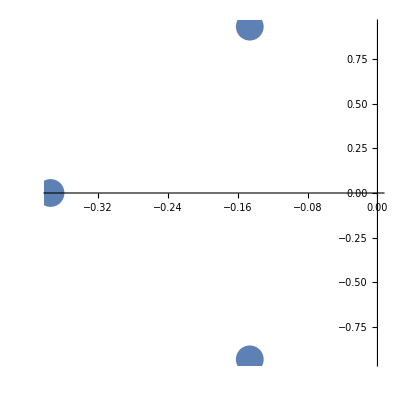

```mathematica
findPlotPoles[tf,<|Ki->1/3,Kd->2/3,Kp->0|>]
```

### Below we have a stable system because none of the poles have a real positive part.

{{s→-0.442493},{s→-0.278753+0.821951 ⅈ},{s→-0.278753-0.821951 ⅈ}}

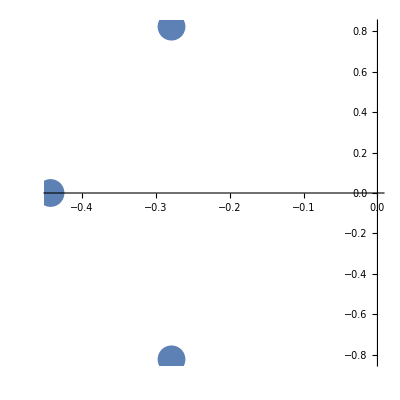

```mathematica
findPlotPoles[tf,<|Ki->1/3,Kd->1,Kp->0|>]
```

```mathematica
tf
```

(Ki+s (Kp+Kd s))/(Ki+s (1+Kp+Kd s+s^2))